## Bidirectional Mother Machine

```mathematica
ClearAll["Global'*"]
Names["Global'*"]
```

{}

### Parameters and Problem

#### We separate our space into N ‘chunks’ that do not have to correspond to cells. Suppose our system is separable into 2 regions where each region has one type of cell. We write our master equation for the boundary when it is at the n^th cell: (dP(n,t))/dt=R_+(n-1)P(n-1,t)+R_-(n+1)P(n+1,t)-[R_+(n)+R_-(n)]P(n,t). What are R_+ and R_-? R_+=(∑_(i=0))^n W_+(i) is the sum of all the rates of cells i ≤ n grow to the right and R_-=(∑_(i=n))^N W_-(i) is the sum of rates that cells i > n grow to the left. W=f(i)=r/(1+(a(i(N_0-i)/N^2))^b)

```mathematica
fixb=2;
params={b->fixb,x0-> 2.0,a->1.0,r->1};
subs={l-> a x0^(2b)};
```

```mathematica
growthRateX=r/(1+a(x (x0-x))^b);
growthRate=r/(1+l(y (1-y))^b);(* y=x/x0, l=a x0^(2b) *)
```

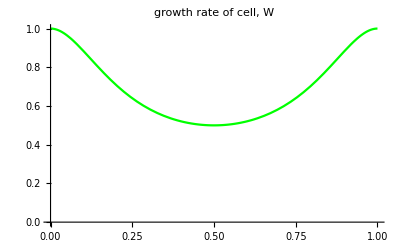

```mathematica
Plot[growthRate/.subs/.params,{y,0.,1},PlotRange-> {{0,1},{0,1}},PlotLabel->"growth rate of cell, W",PlotStyle-> Green]
```

#### The rate that a cell grows f(n) is dependent on the position in the channel, but we’re not too sure how... but here’s an approximation for W=W_++W_-. The rate of growth of a cell is the sum of the rate of growth to the right + rate of growth to the left. As such R=f(n)=R_++R_-=f(n)(n/N+(N-n)/N). One easy choice to find the rate of growth to the right is to simply assume the proportion of cells to the left determine how much it’ll move to the right and vice-versa. W_+(i)=f(i) i/N_0 W_-(i)=f(i) ((N_0-i)/N_0)

```mathematica
growthRateRight=growthRate * y;
growthRateLeft=growthRate *(1-y);
```

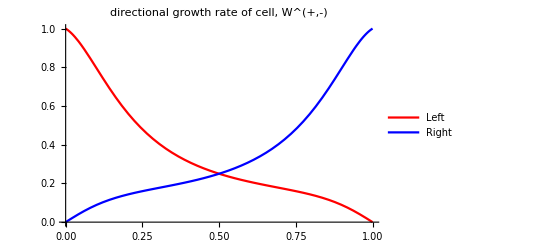

```mathematica
Plot[{growthRateLeft/.subs/.params,growthRateRight/.subs/.params},{y,0.,1},PlotRange-> {{0,1},{0,1}},PlotLegends->{"Left","Right"},PlotLabel->"directional growth rate of cell, W^(+,-)",PlotStyle-> {Red,Blue}]
```

### Boundary Rates

#### Now, we can find the rate of any boundary, j, moving to the right (or left) by summing over all the rate that any cell to the left (or right) divides to the right (or left): R_+(j)=(∑_(i=0))^j f(i) i/N R_-(j)=(∑_(i=j))^N f(i) (N-i)/N This is equivalent to an integral if we take the limit N→∞ .

#### These are the wrong expressions, but Anton did these integrals and I confirm they’re correct

```mathematica
(* gRRpar=FullSimplify[growthRateRight/y/.params];
gRLpar=FullSimplify[growthRateLeft/(1-y)/.params]; *)
```

```mathematica
(* reg=y∈ImplicitRegion[0≤y≤1,y];
Rplus=FullSimplify[Normal[Integrate[gRRpar,{y,0,y},Assumptions->{l>0,y∈Reals}]]];
Rminus=FullSimplify[Normal[Integrate[gRLpar,{y,y,1},Assumptions->{l>0,y∈Reals}]]]; *)
(* A=FullSimplify[ Rplus-Rminus];
B=FullSimplify[ Rplus+Rminus];
AoverB=A/B;*)
```

#### These are the correct expressions

```mathematica
GRRPAR=FullSimplify[growthRateRight/.params];
GRLPAR=FullSimplify[growthRateLeft/.params];
RPLUS=FullSimplify[Normal[Integrate[GRRPAR,{y,0,y},Assumptions->{l>0,y∈Reals}]]]; (*9 mins*)
RMINUS=FullSimplify[Normal[Integrate[GRLPAR,{y,y,1},Assumptions->{l>0,y∈Reals}]]]; (*11 mins *)
```

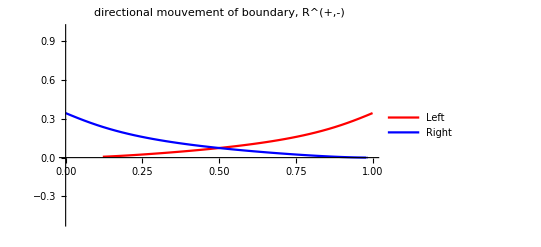

```mathematica
Plot[{RPLUS/.subs/.params,RMINUS/.subs/.params},{y,0.,1},PlotRange-> {{0,1},{-0.5,1}},PlotLegends->{"Left","Right"},PlotLabel->"directional mouvement of boundary, R^(+,-)",PlotStyle-> {Red,Blue}]
```

#### Now we can expand our master to a FP equation and an equivalent backwards FP: (∂P(x,t|x_0,t_0))/(∂t)=A(x_0)(∂P)/(∂x_0)+(B(x_0))/2(∂^2 P)/(∂x_0^2)=L_x_0 P For the probability of exiting to the right P_R(x_0) or left P_L(x_0), solve L_x_0 P_R(x_0)=L_x_0 P_R(x_0)=0 with appropriate boundary condition.

```mathematica
A=Simplify[RPLUS-RMINUS];
B=Simplify[ RPLUS+RMINUS];
AOVERB=Simplify[A/B]; (* No time at all... maybe should try FullSimplify? *)
```

```mathematica
(* Unfortunately, can't seem to integrate P=Integrate[expfg,x] analytically thus need to come up with another scheme to do this *)
(* EXPFG= FullSimplify[Exp[-2 Integrate[AOVERB,y,Assumptions->{l>0,y∈Reals}]]]; *)
```

```mathematica
Clear[phi,phi1,phi2,phi3,phi4,ProbR,ProbL,MFPT]
```

```mathematica
phi[x_?NumericQ]:=phi[x]=Exp[-2 NIntegrate[ AOVERB/.subs/.params,{y,0,x}]];
phi1[x_?NumericQ,a_]:=phi1[x]=Exp[2 NIntegrate[ AOVERB/.subs/.params,{y,a,x}]];
phi2[y1_?NumericQ,a_]:=phi2[y1]=2 NIntegrate[ (phi1[y,a]/B/.subs/.params),{y,a,y1}];
phi3[y2_?NumericQ,a_]:=phi3[y2]=NIntegrate[(1/phi1[y,a])/.subs/.params,{y,a,y2}];
phi4[y3_?NumericQ,a_]:=phi4[y3]=NIntegrate[(phi2[y,a]/phi1[y,a])/.subs/.params,{y,a,y3}];

ProbL[x_?NumericQ,a_,b_]:=NIntegrate[phi[y]/.subs/.params,{y,x,b}]/NIntegrate[phi[y]/.subs/.params,{y,a,b}];
```

```mathematica
MFPT[x_?NumericQ,a_,b_]:=(phi3[x,a]phi4[b,a]-phi3[b,a]phi4[x,a])/phi3[b,a]
```

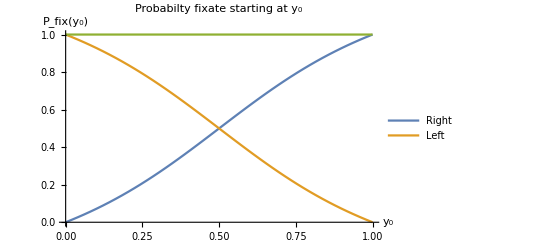

```mathematica
Plot[{ProbR[x,0.0,1.0],ProbL[x,0.0,1.0],ProbR[x,0.0,1.0]+ProbL[x,0.0,1.0]},{x,0.0,1.0},PlotLabel->"Probabilty fixate starting at y_0",PlotLegends->{"Right","Left"},AxesLabel->{"y_0","P_fix(y_0)"}] (* <1 min*)
```

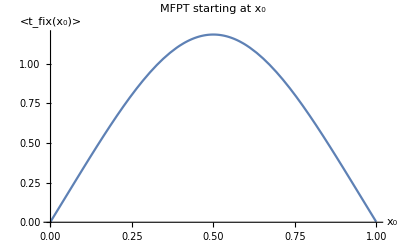

```mathematica
Plot[MFPT[x,0.0,1.0],{x,0.001,0.999},Exclusions->{x==0.,x==1.0},PlotLabel->"MFPT starting at y_0",AxesLabel->{"y_0","<t_fix(y_0)>"}] (* This is long, ~25 mins *)
```

## Other Moran Model type processes

### Analytical

```mathematica
AnaPhi1[fcn_,x_,N_,a_]:=Phi1[fcn,x,N,a]=Exp[2 Integrate[ fcn[y,N],{y,a,x}]];
AnaPhi2[fcn_,B_,x_,N_,a_]:=Phi2[fcn,B,x,N,a]=2 Integrate[ (Phi1[fcn,y,N,a]/B[y,N]),{y,a,x}];
AnaPhi3[fcn_,x_,N_,a_]:=Phi3[fcn,x,N,a]=Integrate[(1/Phi1[fcn,y,N,a]),{y,a,x}];
AnaPhi4[fcn_,B_,x_,N_,a_]:=Phi4[fcn,B,x,N,a]=Integrate[(Phi2[fcn,B,y,N,a]/Phi1[fcn,y,N,a]),{y,a,x}];
AnaProbR[fcn_,x_,N_,a_,b_]:=ProbR[fcn,x,N,a,b]=Integrate[Phi1[fcn,y,N,a],{y,a,x}]/NIntegrate[Phi1[fcn,y,N,a],{y,a,b}];
AnaProbL[fcn_,x_,N_,a_,b_]:=ProbL[fcn,x,N,a,b]=NIntegrate[1/Phi1[fcn,y,N,a],{y,x,b}]/NIntegrate[1/Phi1[fcn,y,N,a],{y,a,b}];
AnaMFPT[fcn_,B_,x_,N_,a_,b_]:=(Phi3[fcn,x,N,a]Phi4[fcn,B,b,N,a]-Phi3[fcn,b,N,a]Phi4[fcn,B,x,N,a])/Phi3[fcn,b,N,a]
```

#### Moran no direction

```mathematica
AnafptMoran[x_,N_]:=-N^2(x Log[x]+(1-x)Log[1-x])
```

#### Moran no direction

```mathematica
AnaMoranNoDA[x_,N_]:=(2 x - 1)/(2 N);
AnaMoranNoDB[x_,N_]:=(2 x^2 -2 x + 1)/(2 N^2);
AnaMoranNoDAoB[x_,N_]:=N *(2 x - 1);
```

#### Moran directional

```mathematica
AnaMoranDA[x_,N_]:=(2 x - 1)/(2 N);
AnaMoranDB[x_,N_]:=(2 x^2 -2 x + 1)/(2 N^2);
AnaMoranDAoB[x_,N_]:=N (2 x - 1)/(2 x^2 -2 x + 1) ;
```

#### Growth Model

```mathematica
AnaMoranDA[x_,N_]:=(2 x - 1)/(2 N);
AnaMoranDB[x_,N_]:=(2 x^2 -2 x + 1)/(2 N^2);
AnaMoranDAoB[x_,N_]:=N (2 x - 1)/(2 x^2 -2 x + 1) ;
```

#### Solving

```mathematica
Solution = AnaProbR[AnaMoranNoDAoB,x,N,0.0,1.0]
AnaBigN=100
(* Try = Integrate[Exp[-2 * N*(-x+x^2)],x];
Something=((Try/.{N-> bigN})-(Try/. {N-> bigN,x-> 0.0}))/((Try/.{N-> bigN,x-> 1.0})-(Try/. {N->bigN,x-> 0.0}));
Something2=((Try/.{N-> bigN,x-> 1.0})-(Try/. {N-> bigN}))/((Try/.{N-> bigN,x-> 1.0})-(Try/. {N-> bigN,x-> 0.0}));*)
Plot[Solution/.N->AnaBigN ,{x,0.0,1.0},PlotLabel->"Probabilty fixate starting at y_0",PlotLegends->{"Right","Left"},AxesLabel->{"y_0","P_fix(y_0)"},PlotRange-> {{0,1},{-0.5,1}}]
```

NIntegrate::inumr: The integrand N (-1+2 y) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,0.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

(∫_0.^x Phi1[AnaMoranNoDAoB,y,N,0.]ⅆy)/NIntegrate[Phi1[AnaMoranNoDAoB,y,N,0.],{y,0.,1.}]

100

NIntegrate::inumr: The integrand N (-1+2 y) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.,0.5}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

-Graphics-

### Numerical

```mathematica
Phi1[fcn_,x_?NumericQ,N_,a_]:=Phi1[fcn,x,N,a]=Exp[2 NIntegrate[ fcn[y,N],{y,a,x}]];
Phi2[fcn_,B_,x_?NumericQ,N_,a_]:=Phi2[fcn,B,x,N,a]=2 NIntegrate[ (Phi1[fcn,y,N,a]/B[y,N]),{y,a,x}];
Phi3[fcn_,x_?NumericQ,N_,a_]:=Phi3[fcn,x,N,a]=NIntegrate[(1/Phi1[fcn,y,N,a]),{y,a,x}];
Phi4[fcn_,B_,x_?NumericQ,N_,a_]:=Phi4[fcn,B,x,N,a]=NIntegrate[(Phi2[fcn,B,y,N,a]/Phi1[fcn,y,N,a]),{y,a,x}];
ProbR[fcn_,x_?NumericQ,N_,a_,b_]:=ProbR[fcn,x,N,a,b]=NIntegrate[Phi1[fcn,y,N,a],{y,a,x}]/NIntegrate[Phi1[fcn,y,N,a],{y,a,b}];
ProbL[fcn_?NumericQ,x_?NumericQ,N_,a_,b_]:=ProbL[fcn,x,N,a,b]=NIntegrate[1/Phi1[fcn,y,N,a],{y,x,b}]/NIntegrate[1/Phi1[fcn,y,N,a],{y,a,b}];
MFPT[fcn_,B_,x_?NumericQ,N_,a_,b_]:=(Phi3[fcn,x,N,a]Phi4[fcn,B,b,N,a]-Phi3[fcn,b,N,a]Phi4[fcn,B,x,N,a])/Phi3[fcn,b,N,a]
```

#### Moran no direction

```mathematica
MfptMoran[x_,N_]:=-N^2(x Log[x]+(1-x)Log[1-x])
```

#### Moran no direction

```mathematica
MoranNoDA[x_,N_]:=(2 x - 1)/(2 N);
MoranNoDB[x_,N_]:=(2 x^2 -2 x + 1)/(2 N^2);
MoranNoDAoB[x_,N_]:=N *(2 x - 1);
```

#### Moran directional

```mathematica
MoranDA[x_,N_]:=(2 x - 1)/(2 N);
MoranDB[x_,N_]:=(2 x^2 -2 x + 1)/(2 N^2);
MoranDAoB[x_,N_]:=N (2 x - 1)/(2 x^2 -2 x + 1) ;
```

#### Growth Model

```mathematica
MoranDA[x_,N_]:=(2 x - 1)/(2 N);
MoranDB[x_,N_]:=(2 x^2 -2 x + 1)/(2 N^2);
MoranDAoB[x_,N_]:=N (2 x - 1)/(2 x^2 -2 x + 1) ;
```

#### Plots

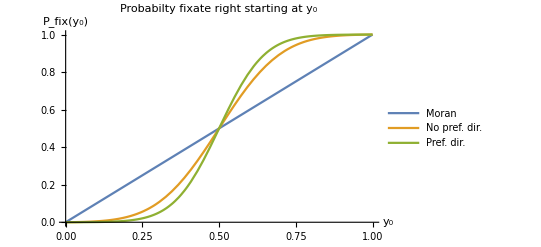

```mathematica
BigN=10;
Plot[{x,ProbR[MoranNoDAoB,x,BigN,0.0,1.0],ProbR[MoranDAoB,x,BigN,0.0,1.0]},{x,0.0,1.0},PlotLabel->"Probabilty fixate right starting at y_0",PlotLegends->{"Moran","No pref. dir.","Pref. dir."},AxesLabel->{"y_0","P_fix(y_0)"},PlotRange-> {{0,1},{0,1}}(* <1 min *)
```

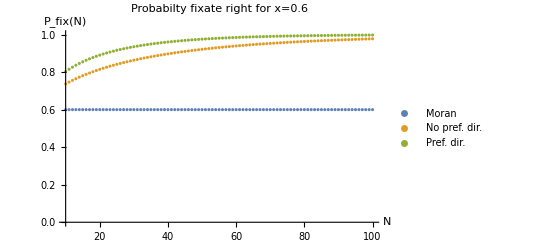

```mathematica
frac1=0.6;
frac2=0.7;
frac3=0.8;
frac4=0.9;
smallN =10;
bigN=100;
DiscretePlot[{frac1,ProbR[MoranNoDAoB,frac1,n,0.0,1.0],ProbR[MoranDAoB,frac1,n,0.0,1.0]},{n,smallN,bigN},Filling-> None,PlotLabel->"Probabilty fixate right for x=0.6",PlotLegends->{"Moran","No pref. dir.","Pref. dir."},AxesLabel->{"N","P_fix(N)"},PlotRange-> {{smallN,bigN},{0,1}}(* <1 min *)
```

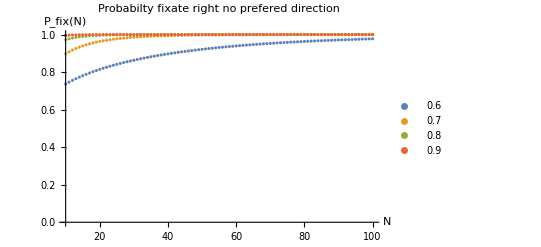

```mathematica
DiscretePlot[{ProbR[MoranNoDAoB,frac1,n,0.0,1.0],ProbR[MoranNoDAoB,frac2,n,0.0,1.0],ProbR[MoranNoDAoB,frac3,n,0.0,1.0],ProbR[MoranNoDAoB,frac4,n,0.0,1.0]},{n,smallN,bigN},Filling-> None,PlotLabel->"Probabilty fixate right - no prefered direction",PlotLegends->{frac1,frac2,frac3,frac4},AxesLabel->{"N","P_fix(N)"},PlotRange-> {{smallN,bigN},{0,1}}(* <1 min *)
```

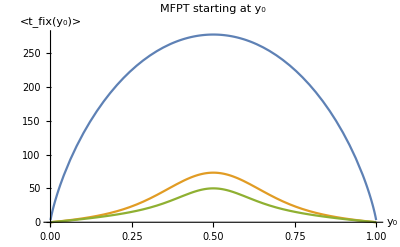

```mathematica
fptN=20;
Plot[{MfptMoran[x,fptN],MFPT[MoranNoDAoB,MoranNoDB,x,fptN,0.0,1.0],MFPT[MoranDAoB,MoranDB,x,fptN,0.0,1.0]},{x,0.001,0.999},Exclusions->{x==0.,x==1.0},PlotLabel->"MFPT starting at y_0",PlotLegends->{"Moran","No pref. dir.","Pref. dir."},AxesLabel->{"y_0","<t_fix(y_0)>"}](* 40mins*)
```

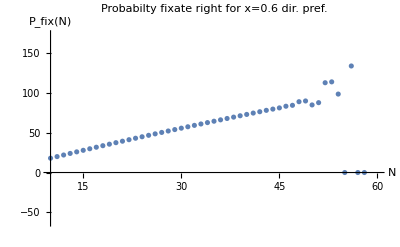

```mathematica
frac=0.6;
smallN =10;
bigN=60;
DiscretePlot[MFPT[MoranDAoB,MoranDB,frac,n,0.0,1.0],{n,smallN,bigN},Filling-> None,PlotLabel->"Probabilty fixate right for x=0.6 dir. pref.",AxesLabel->{"N","P_fix(N)"}]
```

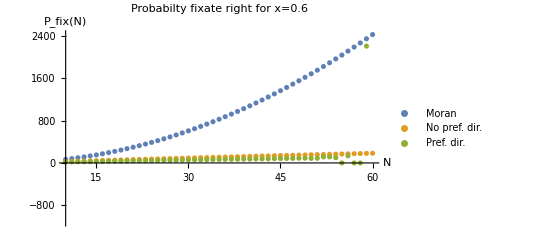

```mathematica
frac1=0.6;
frac2=0.7;
frac3=0.8;
frac4=0.9;
smallN =10;
bigN=60;
DiscretePlot[{MfptMoran[frac1,n],MFPT[MoranNoDAoB,MoranNoDB,frac1,n,0.0,1.0],MFPT[MoranDAoB,MoranDB,frac1,n,0.0,1.0]},{n,smallN,bigN},Filling-> None,PlotLabel->"Probabilty fixate right for x=0.6",PlotLegends->{"Moran","No pref. dir.","Pref. dir."},AxesLabel->{"N","P_fix(N)"} ]
```